## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/home/mrama/Dropbox/MASSef/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_GAPD_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; _nad,g3p,pi,13dpg,nadh

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 1059.36 | 1035.65
1083.08 | 1/s | 8.9 | 37 | teoa | 0.04 | 
1 | 13dpg | Null
nadh | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; _nad,g3p,pi,13dpg,nadh

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 1059.36 | 1035.65
1083.08 | 1/s | 8.9 | 37 | teoa | 0.04 | 
1 | 13dpg | Null
nadh | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,Overscript[(GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c, GAPD2],((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,Overscript[(GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c, GAPD4],((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((GAPD^c&nad^c&g3p^c&pi^c)_^-((GAPD^c&nadh^c&(13dpg)^c)_^)/K_GAPD6) Volume_c k_GAPD6^⟶}

Volume_c (-(GAPD^c&nadh^c&(13dpg)^c)_^ k_GAPD6^⟵+(GAPD^c&nad^c&g3p^c&pi^c)_^ k_GAPD6^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateFor.txt"	1059.363016156407
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	1	0	0	1	0	1	7	37	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_GAPD_MASSpy_typeII\input\customRatio_1.txt"	425.

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\KdRatio_nad.txt, C:\\MASSef\\examples\\fit_GAPD_MASSpy_typeII\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\KdRatio_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.9807736921114941
best_fit: 1.0822752706749703
best_fit: 4.3024892482766095
best_fit: 1.03935152228146
best_fit: 1.040874625244381
best_fit: 1.0624941366357765
best_fit: 1.0994738528974144
best_fit: 1.0970786885802908
best_fit: 4.468845036701412
best_fit: 4.385407853156626

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | haldaneRatio_1 | 0.000265537 | 7.05098×10^-8 | 0.000276278 | 0.0611234 | 0.452 | 0.451724
1 | relRateFor_nad | 0.309967 | 0.0960794 | 0.0946892 | 104.158 | 0.0909091 | 0.185598
1 | relRateFor_nad | 0.28771 | 0.0827768 | 0.128542 | 93.9589 | 0.136807 | 0.265349
1 | relRateFor_nad | 0.258484 | 0.066814 | 0.16329 | 81.336 | 0.20076 | 0.36405
1 | relRateFor_nad | 0.222867 | 0.0496698 | 0.190946 | 67.058 | 0.284747 | 0.475693
1 | relRateFor_nad | 0.183162 | 0.0335485 | 0.202957 | 52.4623 | 0.386863 | 0.58982
1 | relRateFor_nad | 0.143036 | 0.0204592 | 0.195033 | 39.0066 | 0.5 | 0.695033
1 | relRateFor_nad | 0.106305 | 0.0113007 | 0.170044 | 27.7335 | 0.613137 | 0.783181
1 | relRateFor_nad | 0.0756247 | 0.0057191 | 0.13605 | 19.0213 | 0.715253 | 0.851303
1 | relRateFor_nad | 0.0519209 | 0.00269578 | 0.101497 | 12.6992 | 0.79924 | 0.900737
1 | relRateFor_nad | 0.0347009 | 0.00120416 | 0.0718011 | 8.31808 | 0.863193 | 0.934994
1 | relRateFor_nad | 0.0227503 | 0.000517577 | 0.0488917 | 5.37809 | 0.909091 | 0.957983
1 | relRateFor_g3p | 0.000845758 | 7.15306×10^-7 | 0.000177212 | 0.194933 | 0.0909091 | 0.0910863
1 | relRateFor_g3p | 0.000822529 | 6.76554×10^-7 | 0.00025935 | 0.189574 | 0.136807 | 0.137066
1 | relRateFor_g3p | 0.000790165 | 6.2436×10^-7 | 0.0003656 | 0.182108 | 0.20076 | 0.201126
1 | relRateFor_g3p | 0.000747665 | 5.59003×10^-7 | 0.000490633 | 0.172305 | 0.284747 | 0.285238
1 | relRateFor_g3p | 0.000695998 | 4.84413×10^-7 | 0.000620482 | 0.160388 | 0.386863 | 0.387484
1 | relRateFor_g3p | 0.000638762 | 4.08017×10^-7 | 0.000735943 | 0.147189 | 0.5 | 0.500736
1 | relRateFor_g3p | 0.000581533 | 3.38181×10^-7 | 0.000821558 | 0.133993 | 0.613137 | 0.613958
1 | relRateFor_g3p | 0.000529886 | 2.80779×10^-7 | 0.000873217 | 0.122085 | 0.715253 | 0.716126
1 | relRateFor_g3p | 0.000487412 | 2.3757×10^-7 | 0.000897496 | 0.112294 | 0.79924 | 0.800137
1 | relRateFor_g3p | 0.000455072 | 2.07091×10^-7 | 0.000904965 | 0.104839 | 0.863193 | 0.864098
1 | relRateFor_g3p | 0.000431864 | 1.86507×10^-7 | 0.000904454 | 0.0994899 | 0.909091 | 0.909995
1 | relRateFor_pi | 0.00081446 | 6.63346×10^-7 | 0.000170648 | 0.187712 | 0.0909091 | 0.0910797
1 | relRateFor_pi | 0.000784922 | 6.16103×10^-7 | 0.000247482 | 0.180898 | 0.136807 | 0.137054
1 | relRateFor_pi | 0.000743768 | 5.5319×10^-7 | 0.000344114 | 0.171406 | 0.20076 | 0.201104
1 | relRateFor_pi | 0.000689727 | 4.75723×10^-7 | 0.000452582 | 0.158942 | 0.284747 | 0.2852
1 | relRateFor_pi | 0.00062403 | 3.89413×10^-7 | 0.000556276 | 0.143791 | 0.386863 | 0.387419
1 | relRateFor_pi | 0.000551254 | 3.03881×10^-7 | 0.000635058 | 0.127012 | 0.5 | 0.500635
1 | relRateFor_pi | 0.000478491 | 2.28954×10^-7 | 0.000675906 | 0.110237 | 0.613137 | 0.613813
1 | relRateFor_pi | 0.000412826 | 1.70426×10^-7 | 0.00068022 | 0.095102 | 0.715253 | 0.715933
1 | relRateFor_pi | 0.000358827 | 1.28757×10^-7 | 0.000660628 | 0.082657 | 0.79924 | 0.799901
1 | relRateFor_pi | 0.000317712 | 1.00941×10^-7 | 0.000631708 | 0.0731827 | 0.863193 | 0.863825
1 | relRateFor_pi | 0.000288208 | 8.30637×10^-8 | 0.000603494 | 0.0663843 | 0.909091 | 0.909694
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateFor | 0.0823943 | 0.00678881 | 221.312 | 20.8911 | 1059.36 | 1280.68
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | absRateRev | 0.082342 | 0.00678021 | 5.18614 | 17.271 | 30.0281 | 24.842
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | KdRatio_nad | 0.0823564 | 0.00678258 | 6.68177×10^-8 | 20.8805 | 3.2×10^-7 | 3.86818×10^-7
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736
1 | customRatio_1 | 0.000269501 | 7.26308×10^-8 | 0.263652 | 0.0620357 | 425. | 424.736

### Simulated Data and Best Fit Data Plot

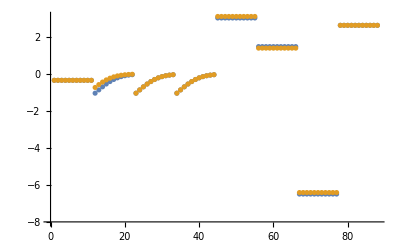

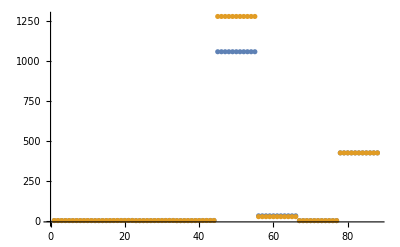

```mathematica
dataSetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

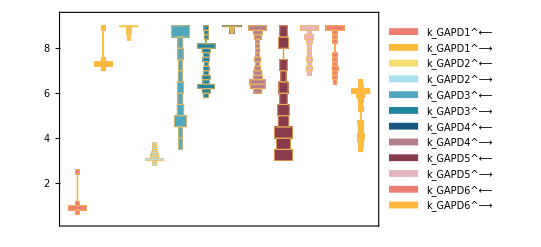

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

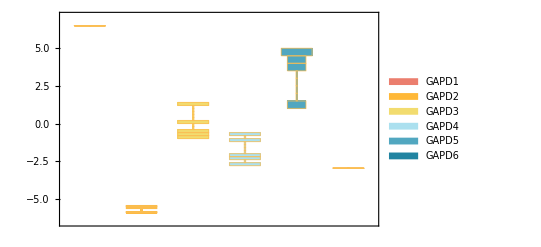

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

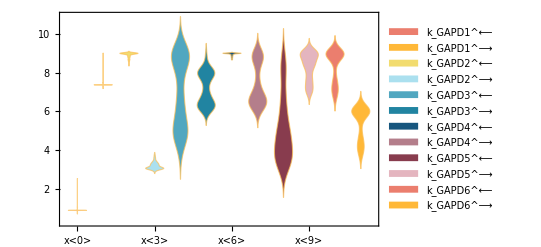

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

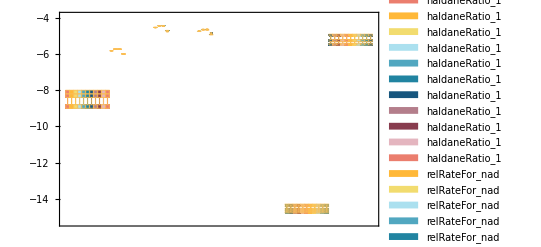

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

0.504033 | 6.84334 | 9. | 3.48477 | 3.72945 | 5.60742 | 8.98508 | 2.55274 | 8.71335 | 6.81329 | 3.3998 | 8.6853
0.302665 | 6.83612 | 9. | 2.49847 | 3.41773 | 5.57282 | 8.4452 | 8.21223 | 8.48635 | 9. | 8.72988 | 5.91734
0.403565 | 6.84537 | 8.93702 | 2.89026 | 3.79923 | 5.61764 | 8.93001 | 2.9612 | 4.37591 | 7.10803 | 2.61941 | 3.29776
0.596512 | 6.9085 | 8.99485 | 2.61851 | 5.40864 | 6.11723 | 8.99485 | 4.0603 | 2.01656 | 6.35182 | 7.98972 | 7.59992
0.530106 | 6.83522 | 8.99996 | 2.63507 | 3.36523 | 5.56857 | 9. | 3.06996 | 4.14564 | 5.88599 | 6.34476 | 8.04601

#### Parameter Cluster Plots (Optional)

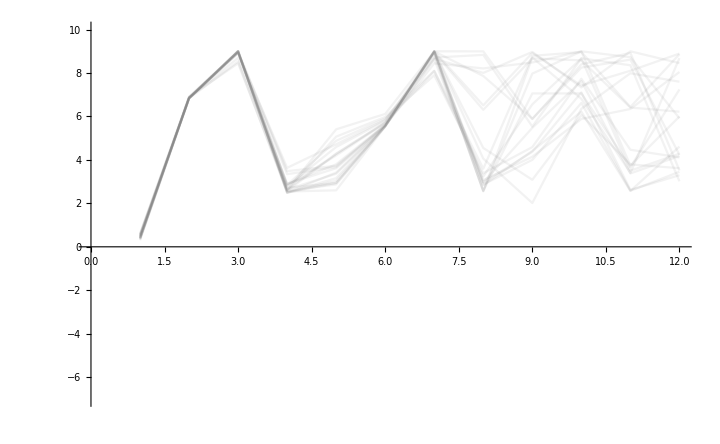

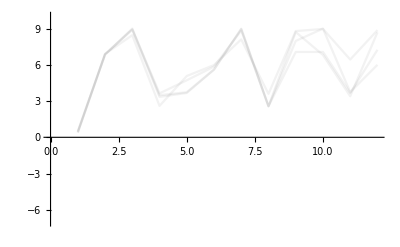
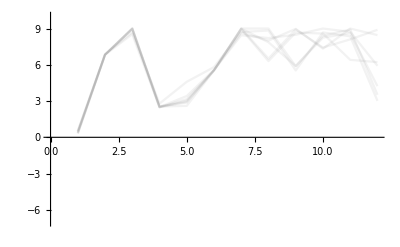
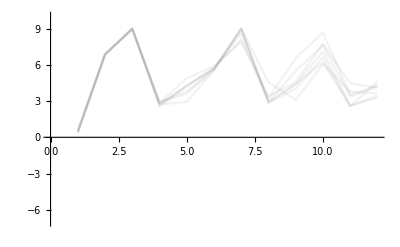
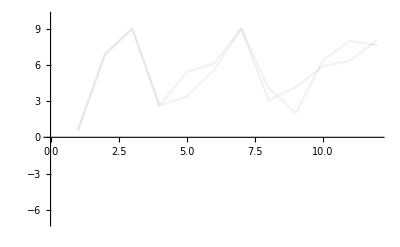

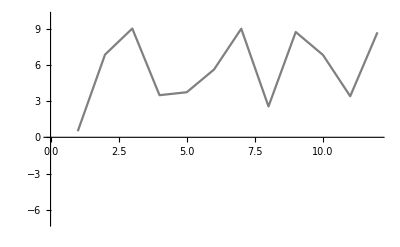
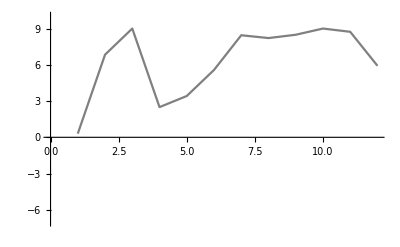
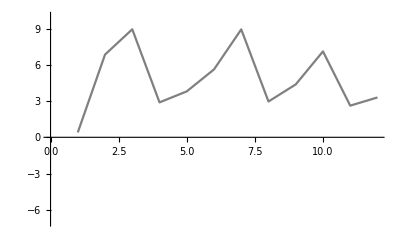

```mathematica
ListPlot[Log10[filteredDataListRed[[All,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000045 | 0.000044999 | 0.00221258
0.00089 | 0.00088961 | 0.0437753
0.00053 | 0.000529862 | 0.0260516

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
1059.36 | 1059.36 | 9.69228×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

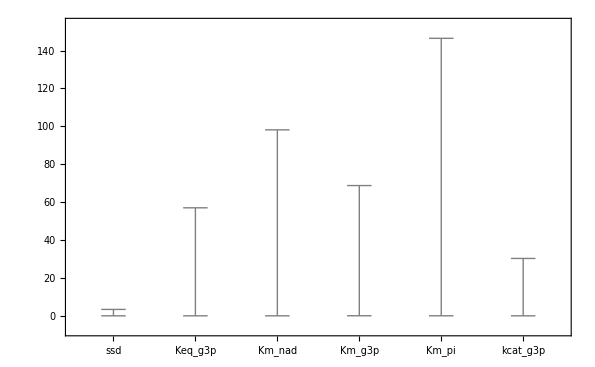

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "C:\\Users\\Daniel Zielinski\\Desktop\\MASSpy Work\\"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 7;
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\

CreateDirectory::filex: C:\Users\Daniel Zielinski\Desktop\MASSpy Work\gapd already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\gapd\rateconst_labels_gapd.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\gapd\S_gapd.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_GAPD[c],E_GAPD[c]&nad,E_GAPD[c]&nadh,E_GAPD[c]&nad&g3p,E_GAPD[c]&nadh&13dpg,13dpg[c],g3p[c],nad[c],nadh[c],pi[c],E_GAPD[c]&nad&g3p&pi}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\gapd\species_gapd.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{GAPD1: E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad,GAPD2: E_GAPD[c]&nadh <=> E_GAPD[c] + nadh[c],GAPD3: E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p,GAPD4: E_GAPD[c]&nadh&13dpg <=> 13dpg[c] + E_GAPD[c]&nadh,GAPD5: E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi,GAPD6: E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\gapd\reactions_gapd.txt

```mathematica
solEnz = Import["C:/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_GAPD[c],E_GAPD[c]&nad,E_GAPD[c]&nadh,E_GAPD[c]&nad&g3p,E_GAPD[c]&nadh&13dpg,E_GAPD[c]&nad&g3p&pi}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_GAPD1_rev*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD5_rev*param_GAPD_total) - k_GAPD1_rev*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD6_fwd*param_GAPD_total - k_GAPD1_rev*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD5_rev*k_GAPD6_rev*param_GAPD_total - 13dpg(c)*k_GAPD1_rev*k_GAPD3_rev*k_GAPD4_rev*k_GAPD5_rev*k_GAPD6_rev*param_GAPD_total - k_GAPD1_rev*k_GAPD2_fwd*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*param_GAPD_total*pi(c) - g3p(c)*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*param_GAPD_total*pi(c))/(k_GAPD1_rev*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD5_rev + k_GAPD1_rev*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD6_fwd + k_GAPD1_rev*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD5_rev*k_GAPD6_rev + 13dpg(c)*k_GAPD1_rev*k_GAPD3_rev*k_GAPD4_rev*k_GAPD5_rev*k_GAPD6_rev + g3p(c)*k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD4_fwd*k_GAPD5_rev*nad(c) + k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD5_rev*nad(c) + g3p(c)*k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD4_fwd*k_GAPD6_fwd*nad(c) + k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD6_fwd*nad(c) + g3p(c)*k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD5_rev*k_GAPD6_rev*nad(c) + k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_rev*k_GAPD5_rev*k_GAPD6_rev*nad(c) + 13dpg(c)*g3p(c)*k_GAPD1_fwd*k_GAPD3_fwd*k_GAPD4_rev*k_GAPD5_rev*k_GAPD6_rev*nad(c) + 13dpg(c)*k_GAPD1_fwd*k_GAPD3_rev*k_GAPD4_rev*k_GAPD5_rev*k_GAPD6_rev*nad(c) + k_GAPD1_rev*k_GAPD2_rev*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD5_rev*nadh(c) + 13dpg(c)*k_GAPD1_rev*k_GAPD2_rev*k_GAPD3_rev*k_GAPD4_rev*k_GAPD5_rev*nadh(c) + k_GAPD1_rev*k_GAPD2_rev*k_GAPD3_rev*k_GAPD4_fwd*k_GAPD6_fwd*nadh(c) + 13dpg(c)*k_GAPD1_rev*k_GAPD2_rev*k_GAPD3_rev*k_GAPD4_rev*k_GAPD6_fwd*nadh(c) + 13dpg(c)*k_GAPD1_rev*k_GAPD2_rev*k_GAPD3_rev*k_GAPD4_rev*k_GAPD6_rev*nadh(c) + k_GAPD1_rev*k_GAPD2_rev*k_GAPD3_rev*k_GAPD5_rev*k_GAPD6_rev*nadh(c) + 13dpg(c)*k_GAPD1_rev*k_GAPD2_rev*k_GAPD4_rev*k_GAPD5_rev*k_GAPD6_rev*nadh(c) + 13dpg(c)*g3p(c)*k_GAPD2_rev*k_GAPD3_fwd*k_GAPD4_rev*k_GAPD5_rev*k_GAPD6_rev*nadh(c) + 13dpg(c)*k_GAPD2_rev*k_GAPD3_rev*k_GAPD4_rev*k_GAPD5_rev*k_GAPD6_rev*nadh(c) + k_GAPD1_rev*k_GAPD2_fwd*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*pi(c) + g3p(c)*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*pi(c) + g3p(c)*k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD4_fwd*k_GAPD5_fwd*nad(c)*pi(c) + g3p(c)*k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD5_fwd*k_GAPD6_fwd*nad(c)*pi(c) + k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*nad(c)*pi(c) + g3p(c)*k_GAPD1_fwd*k_GAPD3_fwd*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*nad(c)*pi(c) + 13dpg(c)*g3p(c)*k_GAPD1_fwd*k_GAPD3_fwd*k_GAPD4_rev*k_GAPD5_fwd*k_GAPD6_fwd*nad(c)*pi(c) + g3p(c)*k_GAPD1_fwd*k_GAPD2_fwd*k_GAPD3_fwd*k_GAPD5_fwd*k_GAPD6_rev*nad(c)*pi(c) + 13dpg(c)*g3p(c)*k_GAPD1_fwd*k_GAPD3_fwd*k_GAPD4_rev*k_GAPD5_fwd*k_GAPD6_rev*nad(c)*pi(c) + k_GAPD1_rev*k_GAPD2_rev*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*nadh(c)*pi(c) + g3p(c)*k_GAPD2_rev*k_GAPD3_fwd*k_GAPD4_fwd*k_GAPD5_fwd*k_GAPD6_fwd*nadh(c)*pi(c) + 13dpg(c)*k_GAPD1_rev*k_GAPD2_rev*k_GAPD4_rev*k_GAPD5_fwd*k_GAPD6_fwd*nadh(c)*pi(c) + 13dpg(c)*g3p(c)*k_GAPD2_rev*k_GAPD3_fwd*k_GAPD4_rev*k_GAPD5_fwd*k_GAPD6_fwd*nadh(c)*pi(c) + 13dpg(c)*k_GAPD1_rev*k_GAPD2_rev*k_GAPD4_rev*k_GAPD5_fwd*k_GAPD6_rev*nadh(c)*pi(c) + 13dpg(c)*g3p(c)*k_GAPD2_rev*k_GAPD3_fwd*k_GAPD4_rev*k_GAPD5_fwd*k_GAPD6_rev*nadh(c)*pi(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\gapd\rateconst_clusters_gapd.txt

```mathematica
solRateEq = Import["C:/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\gapd\rateLaw_gapd.txt